Tyson Jones, 5th July 2018
tyson.jones@materials.ox.ac.uk

## Code

Here’s the setup, you can skip this

### Gates

#### Single qubit

```mathematica
gateH = 1/(√2)({{1, 1}, {1, -1}});
gateX = ({{0, 1}, {1, 0}});
gateY = ({{0, -ⅈ}, {ⅈ, 0}});
gateZ = ({{1, 0}, {0, -1}});
gateI = ({{1, 0}, {0, 1}});
gateRx[θ_] = ({{Cos[θ/2], -ⅈ Sin[θ/2]}, {-ⅈ Sin[θ/2], Cos[θ/2]}});
gateRy[θ_] = ({{Cos[θ/2], -Sin[θ/2]}, {Sin[θ/2], Cos[θ/2]}});
gateRz[θ_] = ({{Exp[-ⅈ θ/2], 0}, {0, Exp[ⅈ θ/2]}});
```

```mathematica
(* turns matrix A into I ⊕ I ⊕ ... ⊕ A ⊕ I ⊕ ... *)
expandSingle[singleQubitMatrix_, qubitIndex_, numQubits_] :=
	KroneckerProduct[
		IdentityMatrix[ 2^qubitIndex ],
		singleQubitMatrix,
		IdentityMatrix[ 2^(numQubits - qubitIndex - 1) ]
	]
```

#### Control qubit

```mathematica
adjSwapGate = ( {{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
adjControlGate[gate_] := ( {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}) + KroneckerProduct[({{0, 0}, {0, 1}}), gate];
```

```mathematica
(* turns matrix A⊕B into I ⊕ I ⊕ ... ⊕ A⊕B ⊕ I ⊕ ... *)
expandDouble[doubleQubitMatrix_, firstQubitIndex_, numQubits_] :=
	KroneckerProduct[
		IdentityMatrix[ 2^firstQubitIndex ],
		doubleQubitMatrix,
		IdentityMatrix[ 2^(numQubits - firstQubitIndex - 2) ]
	]
	
(* swaps q0 with q0+1, q0+1 with q0+2, ..., q1-1 with q1 *)
expandSwapsBetweenQubits[q0_, q1_, numQubits_] :=
	Dot @@ Table[
		expandDouble[adjSwapGate, t, numQubits],
		{t, Min[q0,q1], Max[q0,q1]-1}
	]
	
(* control applies gate by temporarily moving control and target to 0 and 1 inds *)
nonAdjControlGate[gate_, ctrl_, targ_, numQubits_] := 
	expandSwapsBetweenQubits[0, ctrl, numQubits] .
	expandSwapsBetweenQubits[1, targ, numQubits] . 
	expandDouble[adjControlGate[gate], 0, numQubits] .
	expandSwapsBetweenQubits[1, targ, numQubits] . 
	expandSwapsBetweenQubits[0, ctrl, numQubits]
```

### States

#### Classical

```mathematica
(* builds computational states *)
getClassicalKetState[ind_, numQubits_] :=
	Table[{If[t===ind,1,0]},{t,0,2^numQubits-1}]
getClassicalBraState[ind_, numQubits_] :=
	Table[If[t===ind,1,0],{t,0,2^numQubits-1}]
```

### Interface

```mathematica
(* disables gate commutivity, replaces Times with Dot *)
$Pre = 
  Function[{arg}, 
   ReleaseHold[
    Hold[arg] //.  
     Times[α___, 
       patt : (Longest[(Subscript[_Symbol, _Integer]|Subscript[_Symbol, _Integer][___]|_Integer|_Integer) ..]), ω___] :> 
      Times[α, Dot[patt], ω]], HoldAll];
```

```mathematica
(* recognising gates *)
evalRules = {
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ_Integer]] :> nonAdjControlGate[
		Symbol@StringJoin["gate",ToString@gate], 
		ctrl, targ, NUMQUBITS],
	Subscript[C, ctrl_Integer][Subscript[gate_Symbol, targ__Integer][args__]] :> nonAdjControlGate[ 
		Symbol[StringJoin["gate",ToString@gate]][args], 
		ctrl, targ, NUMQUBITS],
	Subscript[H, ind_Integer]:> expandSingle[gateH, ind, NUMQUBITS],
	Subscript[X, ind_Integer] :> expandSingle[gateX, ind, NUMQUBITS],
	Subscript[Y, ind_Integer] :> expandSingle[gateY, ind, NUMQUBITS],
	Subscript[Z, ind_Integer] :> expandSingle[gateZ, ind, NUMQUBITS],
	Subscript[Id, ind_Integer]:> expandSingle[gateI, ind, NUMQUBITS],
	Subscript[Rx, ind_Integer][θ_] :> expandSingle[gateRx[θ], ind, NUMQUBITS],
	Subscript[Ry, ind_Integer][θ_] :> expandSingle[gateRy[θ], ind, NUMQUBITS],
	Subscript[Rz, ind_Integer][θ_] :> expandSingle[gateRz[θ], ind, NUMQUBITS],
	ind_Integer :> getClassicalKetState[ind, NUMQUBITS],
	ind_Integer :> getClassicalBraState[ind, NUMQUBITS]
};
```

```mathematica
(* substitutes gates for matrices, inferring the number of qubits *)
eval[terms_] :=
	With[
		{numQubits = Max[
			1 + Cases[{terms}, Subscript[gate_, ind_]-> ind, ∞],      (* simple gates *)
			1 + Cases[{terms}, Subscript[gate_, ind_][___] -> ind, ∞],  (* gates with args *)
			Cases[{terms}, (state_Integer|state_Integer) :> Ceiling @ N @ Log2[state+1], ∞]
		]},
		terms /. (evalRules /. NUMQUBITS -> numQubits)
	]
```

## Usage

Defined gates: H, X, Y, Z, Rx, Ry, Rz, C

Symbols with subscripts (ctrl - minus) are assumed to be non-commutative gates and have multiplication changed to inner products.

```mathematica
Subscript[H, 0] Subscript[Y, 2]+ α Subscript[Z, 1] Subscript[Rz, 0][θ]
```

H_0.Y_2+α Z_1.Rz_0[θ]

The subscript integer specifies the qubit on which to act the gate.
The eval function substitutes gates for matrices

```mathematica
eval[%] // MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) α | -ⅈ/(√2) | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0
ⅈ/(√2) | ⅇ^(-(ⅈ θ)/2) α | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0
0 | 0 | -ⅇ^(-(ⅈ θ)/2) α | -ⅈ/(√2) | 0 | 0 | 0 | -ⅈ/(√2)
0 | 0 | ⅈ/(√2) | -ⅇ^(-(ⅈ θ)/2) α | 0 | 0 | ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 0 | 0 | ⅇ^((ⅈ θ)/2) α | ⅈ/(√2) | 0 | 0
ⅈ/(√2) | 0 | 0 | 0 | -ⅈ/(√2) | ⅇ^((ⅈ θ)/2) α | 0 | 0
0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | -ⅇ^((ⅈ θ)/2) α | ⅈ/(√2)
0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | -ⅈ/(√2) | -ⅇ^((ⅈ θ)/2) α)

Controls C can wrap any single gate, where the subscript specifies the control qubit. 
Bra and Ket of an integer n produce the nth classical state

```mathematica
Subscript[C, 0][Subscript[X, 1]] Subscript[H, 0] 0 // eval
1 Subscript[X, 0] 0  // eval
```

{{1/(√2)},{0},{0},{1/(√2)}}

{1}

The total number of qubit is inferred from the maximum index / classical state

```mathematica
Subscript[X, 0] Subscript[Y, 1]// eval // MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

```mathematica
Subscript[X, 0] Subscript[Y, 3]// eval // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[H, 0] 10  // eval // MatrixForm
```

(0
0
1/(√2)
0
0
0
0
0
0
0
-1/(√2)
0
0
0
0
0)

You can use the identity gate Id to force a great number of qubits

```mathematica
Subscript[X, 0] // eval
Subscript[X, 0] Subscript[Id, 2] // eval
```

{{0,1},{1,0}}

{{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}}

## Pitfalls

Automatic conversion of gate multiplication to dot products...

```mathematica
Subscript[H, 0] Subscript[H, 1]
```

H_0.H_1

doesn’t automatically distribute

```mathematica
(Subscript[H, 0] + Subscript[H, 1]) Subscript[H, 2]  // Expand
```

H_0 H_2+H_1 H_2

and eval will treat the multiplication as element wise (rather than matrix multiplication)

```mathematica
%  // eval
```

{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,1}}

To remedy, replace every multiplication with a dot product

```mathematica
(Subscript[H, 0] + Subscript[H, 1]) . Subscript[H, 2] // eval
```

{{1,1,1/2,1/2,1/2,1/2,0,0},{1,-1,1/2,-1/2,1/2,-1/2,0,0},{1/2,1/2,0,0,0,0,1/2,1/2},{1/2,-1/2,0,0,0,0,1/2,-1/2},{1/2,1/2,0,0,0,0,1/2,1/2},{1/2,-1/2,0,0,0,0,1/2,-1/2},{0,0,1/2,1/2,1/2,1/2,-1,-1},{0,0,1/2,-1/2,1/2,-1/2,-1,1}}

This applies to Bras and Kets too

```mathematica
(a 0 + b 1 )  Subscript[H, 1]  0  // eval    (* expansion won't convert to dot *)
(a 0 + b 1 ) .  Subscript[H, 1]  0  // eval  (* ALL multiplication must be replaced to dot *)
(a 0 + b 1 ) .  Subscript[H, 1] . 0  // eval
```

{{a/(√2)},{b/(√2)},{0},{0}}

{{a/(√2)+b/(√2)},{0},{0},{0}}

{a/(√2)+b/(√2)}

Bra and Ket will not automatically outer-product

```mathematica
3 1  // eval
```

Dot::dotsh: Tensors {{0},{0},{0},{1}} and {0,1,0,0} have incompatible shapes.

{{0},{0},{0},{1}}.{0,1,0,0}

```mathematica
3 ⊗ 1 // eval // MatrixForm
```

((0
0
0
0)
(0
0
0
0)
(0
0
0
0)
(0
1
0
0))

## Examples

```mathematica
Subscript[C, 0][Subscript[X, 1]] Subscript[H, 0] 0  + Subscript[Y, 0] Subscript[Rz, 1][θ] 3   // eval 
(α 1 + β 2 + γ 3) .  % // eval
```

{{1/(√2)},{-ⅈ ⅇ^((ⅈ θ)/2)},{0},{1/(√2)}}

{-ⅈ ⅇ^((ⅈ θ)/2) α+γ/(√2)}

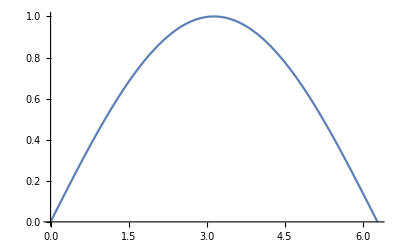

```mathematica
Plot[
	1 Subscript[Ry, 0][θ] 0 // eval,
	{θ, 0, 2π}
]
```

```mathematica
f[a]/(√2) Subscript[C, 0][Subscript[Rz, 1][b]] Subscript[H, 0] Subscript[Ry, 1][a] + g Subscript[C, 1][Subscript[H, 0]] Subscript[Y, 1]   // eval // MatrixForm
```

(1/2 Cos[a/2] f[a] | -ⅈ g-1/2 f[a] Sin[a/2] | 1/2 Cos[a/2] f[a] | -1/2 f[a] Sin[a/2]
ⅈ g+1/2 f[a] Sin[a/2] | 1/2 Cos[a/2] f[a] | 1/2 f[a] Sin[a/2] | 1/2 Cos[a/2] f[a]
1/2 ⅇ^(-(ⅈ b)/2) Cos[a/2] f[a] | -1/2 ⅇ^(-(ⅈ b)/2) f[a] Sin[a/2] | (ⅈ g)/(√2)-1/2 ⅇ^(-(ⅈ b)/2) Cos[a/2] f[a] | -(ⅈ g)/(√2)+1/2 ⅇ^(-(ⅈ b)/2) f[a] Sin[a/2]
1/2 ⅇ^((ⅈ b)/2) f[a] Sin[a/2] | 1/2 ⅇ^((ⅈ b)/2) Cos[a/2] f[a] | -(ⅈ g)/(√2)-1/2 ⅇ^((ⅈ b)/2) f[a] Sin[a/2] | -(ⅈ g)/(√2)-1/2 ⅇ^((ⅈ b)/2) Cos[a/2] f[a])